## Объявление глобальных переменных

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.01;horizSize=0.03;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

## Построение одного графика

### Импорт табличных данных

```mathematica
data=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/4sem/421/tables/rings.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
data//TableForm
```

m | l1 т | l2 т | r_m^2 | l1 | l2 | r_m’^2
0. | 4.71 | 3.72 | 0.25 | 4.15 | 4.15 | 0.
1. | 5. | 3.24 | 0.77 | 4.78 | 3.43 | 0.46
2. | 5.45 | 2.92 | 1.6 | 5.16 | 3.08 | 1.08
3. | 5.59 | 2.65 | 2.16 | 5.44 | 2.79 | 1.76
4. | 5.83 | 2.42 | 2.91 | 5.7 | 2.54 | 2.5
5. | 6.02 | 2.23 | 3.59 | 5.91 | 2.32 | 3.22
6. | 6.17 | 2.06 | 4.22 | 6.09 | 2.11 | 3.96
7. | 6.47 | 1.89 | 5.24 | 6.25 | 1.97 | 4.58

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[0.13675+0.701847 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.13675 | 0.0762931 | 1.79243 | 0.123238
x | 0.701847 | 0.0182376 | 38.4836 | 2.05607×10^-8

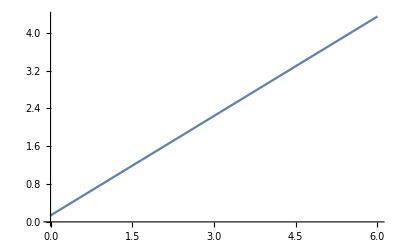

```mathematica
forFitD=data⟦2;;,{1,4}⟧;
fitD=LinearModelFit[forFitD,{1,x},x]
fitD@"ParameterTable"
Plot[fitD["Function"]@x, {x, 0, 6}]
```

FittedModel[-0.170363+0.675496 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.170363 | 0.0641777 | -2.65454 | 0.0377985
x | 0.675496 | 0.0153414 | 44.0309 | 9.18836×10^-9

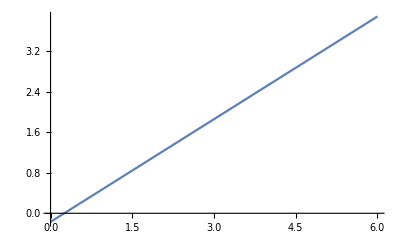

```mathematica
forFitL=data⟦2;;,{1,7}⟧;
fitL=LinearModelFit[forFitL,{1,x},x]
fitL@"ParameterTable"
Plot[fitL["Function"]@x, {x, 0, 6}]
```

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,1}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

### Построение графика линейной функции + табличные данные без крестов

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y}.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

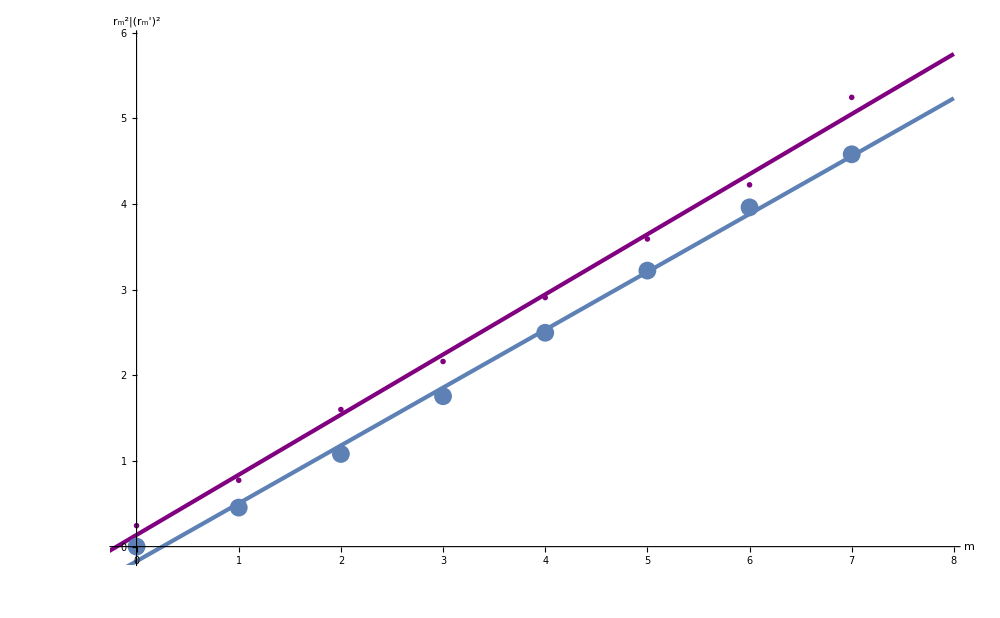

```mathematica
Show[ListPlot[data⟦2;;,{1,4}⟧,
GridLines->{grids@0.25,grids@0.25},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"m","r_m^2|(r_m')^2"},
AxesStyle->Directive[Large,Black],ImageSize->1000,
PlotMarkers->{"◼︎", 30},
PlotStyle->{Purple},
Ticks->{myTicX}, 
PlotRange->{{-0.1,7.9},{-0.1,5.9}}], 
Plot[fitD["Function"]@x,{x,-1,8}, PlotStyle->{Thickness@0.003, Purple}],
ListPlot[data⟦2;;,{1,7}⟧],
Plot[fitL["Function"]@x,{x,-1,8}, PlotStyle->{Thickness@0.003}]]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{1,4,5,5}⟧,
GridLines->{grids@0.5,grids@0.5},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"X","Y"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
(*Ticks->{myTicksX,myTicksY},*)
PlotRange->{{0,6.9},{0,15}}], 
Plot[fit["Function"]@x,{x,0,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX=MapAt[dropLastDot@*ToString,data,{{2;;,All}}];
forTeX//TeXForm
```

\left(
\begin{array}{ccccccc}
 \text{m} & \text{l1 $\unicode{0442}$} & \text{l2 $\unicode{0442}$} & \text{r$\_$m${}^{\wedge}$2} & \text{l1} & \text{l2} & \text{r$\_$m{'}${}^{\wedge}$2}
   \\
 0 & 4.71 & 3.72 & 0.25 & 4.15 & 4.15 & 0 \\
 1 & 5 & 3.24 & 0.77 & 4.78 & 3.43 & 0.46 \\
 2 & 5.45 & 2.92 & 1.6 & 5.16 & 3.08 & 1.08 \\
 3 & 5.59 & 2.65 & 2.16 & 5.44 & 2.79 & 1.76 \\
 4 & 5.83 & 2.42 & 2.91 & 5.7 & 2.54 & 2.5 \\
 5 & 6.02 & 2.23 & 3.59 & 5.91 & 2.32 & 3.22 \\
 6 & 6.17 & 2.06 & 4.22 & 6.09 & 2.11 & 3.96 \\
 7 & 6.47 & 1.89 & 5.24 & 6.25 & 1.97 & 4.58 \\
\end{array}
\right)